```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
dCoords={T,R,Θ,Φ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=+4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=.;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] dCoords[[j]] dCoords[[k]],{j,1,n},{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] dCoords[[j]] dCoords[[k]],{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend=maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[dCoords[[i]]'[τ]==(geodesic[[i]]/.Join[Table[dCoords[[i]]->dCoords[[i]][τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[τ]==dCoords[[i]][τ],{i,1,n}]];
deq=Join[deq,Table[dCoords[[i]][0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,maxτi},Method->{"EventLocator","Event":>(r[τ]≤1.01*rplus),"EventAction":>Throw[τend=τ,"StopIntegration"]}];
soln]
```

```mathematica
hitOrMiss[mτ_,icsin_,αin_,βin_] := Block[{},
x' = Sin[αin]Cos[βin];
y' = Sin[αin]Sin[βin];
z' = Cos[αin];
uθ = x'Sqrt[ϕϕ /. r -> ics[[2]] /. θ -> ics[[3]]];
uϕ = y' Sqrt[θθ /. r-> ics[[2]] /. θ -> ics[[3]]];
ur = -z'Sqrt[rr /. r-> ics[[2]] /. θ -> ics[[3]]];
ivs = {ur,uθ,uϕ};
(*Print[ivs];*)
soln = computeSoln[mτ,ivs,icsin];
If[mτ==τend,0,1]]
```

```mathematica
M=1;a=M;uinvar=0;
ics = {0,5,π/2,0};
hitOrMiss[500,ics,π/10,π/2]
```

1

```mathematica
M=1;a=M;uinvar=0;
ics = {0,5,π/2,0};
αFinal = π/8; αStep = 0.001; βStep=0.05;
noOfPoints = π/8 / αStep * 2π/βStep
points = AbsoluteTiming[Table[
(*If[hitOrMiss[500,ics,α,β]==1,ListPlot[{{Sin[α]Sin[β],Sin[α]Cos[β]}}],ListPlot[{{}}]]*)
If[hitOrMiss[500,ics,α,β]==1,{Sin[α]Sin[β],Sin[α]Cos[β]}]
,{α,0,αFinal,αStep}
,{β,0,2π,βStep}
]];
points[[1]]
```

49348.

2184.14038

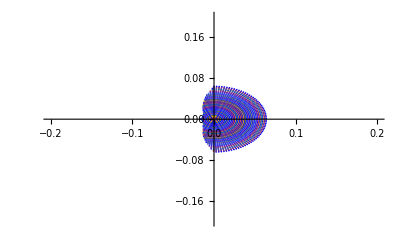

```mathematica
ListPlot[points[[2]],PlotRange->{{-0.2,0.2},{-0.2,0.2}},PlotStyle->{Blue,Thin}]
points[[2]];
```

```mathematica
scanαβ[maxτ_,icsin_] := Block[ {},
Table[{α,β,hitOrMiss[maxτ,icsin,α,β]},
{α,-π/4,π/4,0.1},{β,0,2π,0.1}]]
ics = {0,5,π/2,0};
hitOrMiss[500,ics,1,π/2]
scan=scanαβ[500,ics];
αs=Table[scan[[i,1]][[1]],{i,1,Length[scan],1}];
βs=Table[scan[[1,i]][[2]],{i,1,Length[scan[[1]]],1}];
xyScan = Table[{Sin[αs[[i]]]Cos[βs[[j]]],Sin[αs[[i]]]Sin[βs[[j]]],scan[[i,j,3]]},{i,1,Length[αs]},{j,1,Length[βs]}];
```